alpha→-2.6,beta→1.4,gamma→-0.1

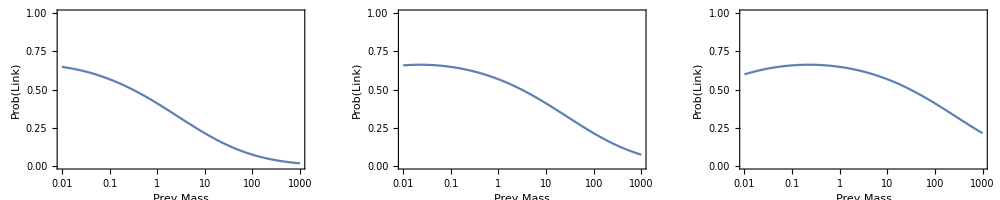

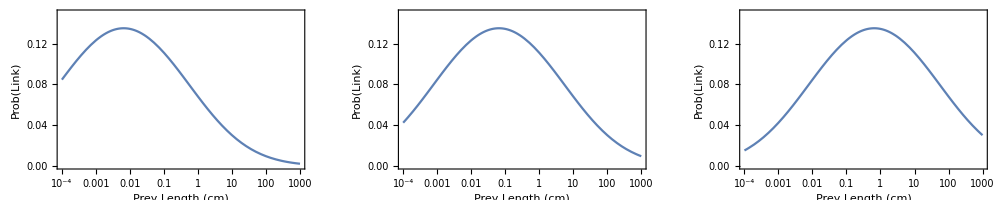

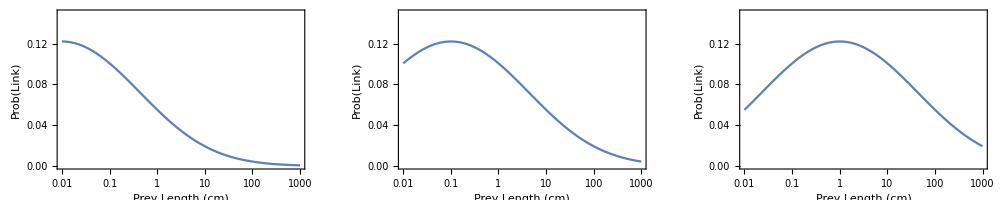

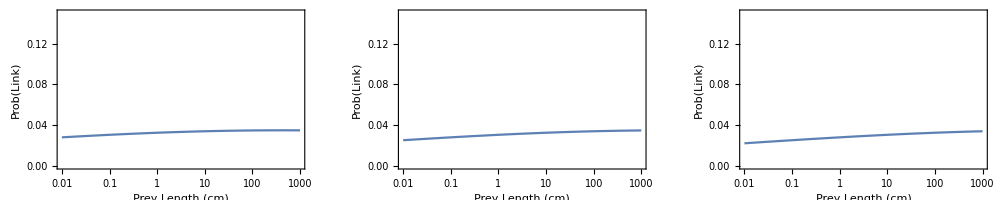

```mathematica
p = Exp[alpha + beta*Log[PredMass/PreyMass] + gamma*Log[PredMass/PreyMass]^2];
prob = p/(1+p);
GraphicsGrid[{Table[LogLinearPlot[prob/.{PredMass->i,alpha->-1.30,beta->0.47,gamma->-0.028},{PreyMass,0.01,1000},PlotRange->{0,1},Frame->True,FrameLabel->{"Prey Mass","Prob(Link)",ToString[{"Pred Mass=",i}]},AspectRatio->0.5,ImageSize->500],{i,{10,100,1000}}]},ImageSize->1000]
GraphicsGrid[{Table[LogLinearPlot[prob/.{PredMass->i,alpha->-3.47,beta->0.44,gamma->-0.03},{PreyMass,0.0001,1000},PlotRange->{0,0.15},Frame->True,FrameLabel->{"Prey Length (cm)","Prob(Link)",ToString[{"Pred Length=",i}]},AspectRatio->0.5,ImageSize->500],{i,{10,100,1000}}]},ImageSize->1000]
GraphicsGrid[{Table[LogLinearPlot[prob/.{PredMass->i,alpha->-3.926,beta->0.566,gamma->-0.041},{PreyMass,0.01,1000},PlotRange->{0,0.15},Frame->True,FrameLabel->{"Prey Length (cm)","Prob(Link)",ToString[{"Pred Length=",i}]},AspectRatio->0.5,ImageSize->500],{i,{10,100,1000}}]},ImageSize->1000]
GraphicsGrid[{Table[LogLinearPlot[prob/.{PredMass->i,alpha->-3.346,beta->-0.015,gamma->-0.002},{PreyMass,0.01,1000},PlotRange->{0,0.15},Frame->True,FrameLabel->{"Prey Length (cm)","Prob(Link)",ToString[{"Pred Length=",i}]},AspectRatio->0.5,ImageSize->500],{i,{10,100,1000}}]},ImageSize->1000]
```

```mathematica
prob/.{PredMass->i,alpha->-3.926,beta->0.566,gamma->-0.041}
```

(ⅇ^(-3.926-0.041 Log[i/PreyMass]^2) (i/PreyMass)^0.566)/(1+ⅇ^(-3.926-0.041 Log[i/PreyMass]^2) (i/PreyMass)^0.566)

```mathematica
NormalizingConstant = NIntegrate[prob/.{PredMass->100,alpha->-3.926,beta->0.566,gamma->-0.041},{PreyMass,0.0001,10000}]
```

22.732

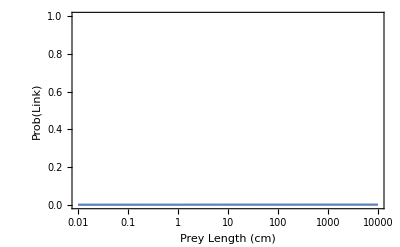

```mathematica
LogLinearPlot[prob/NormalizingConstant/.{PredMass->100,alpha->-3.346,beta->-0.015,gamma->-0.002},{PreyMass,0.01,10000},PlotRange->{0,1},Frame->True,FrameLabel->{"Prey Length (cm)","Prob(Link)"}]
```